```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

```mathematica
PlotTheTest[data_]:=Module[{netPoints, values},
netPoints = data[[1]];
	values = data[[2]];
ListPlot[Table[{netPoints[[i]], values[[i]]},{i,1,Length[netPoints]}],Joined->True, AxesLabel->{"x", "u(x)"}]];
ComparePlotTheTest[d1_, d2_] := Module[{netPoints1, values1,netPoints2, values2},
netPoints1 = d1[[1]];
	values1 = d1[[2]];
netPoints2 = d2[[1]];
	values2 = d2[[2]];
ListPlot[{Table[{netPoints1[[i]], values1[[i]]},{i,1,Length[netPoints1]}],
Table[{netPoints2[[j]], values2[[j]]},{j,1,Length[netPoints2]}]},
Joined->True, AxesLabel->{"x", "u(x)"}]];
Compare3PlotTheTest[d1_, d2_, d3_] := Module[{netPoints1, values1,netPoints2, values2, netPoints3, values3},
netPoints1 = d1[[1]];
	values1 = d1[[2]];
netPoints2 = d2[[1]];
	values2 = d2[[2]];
netPoints3 = d3[[1]];
	values3 = d3[[2]];
ListPlot[{Table[{netPoints1[[i]], values1[[i]]},{i,1,Length[netPoints1]}],
Table[{netPoints2[[j]], values2[[j]]},{j,1,Length[netPoints2]}], Table[{netPoints3[[i]], values3[[i]]},{i,1,Length[netPoints3]}]},
Joined->True, AxesLabel->{"x", "u(x)"}]];
```

## Часть 1: квадратуры и итерации

Тест 1

Метод квадратур

```mathematica
QuaData1 = Import["QuadtratureTest1.txt", "Table"];
```

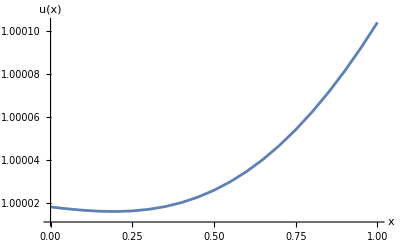

```mathematica
PlotTheTest[QuaData1 ]
```

Итерационный метод

```mathematica
IteData1 = Import["IterativeTest1.txt", "Table"];
```

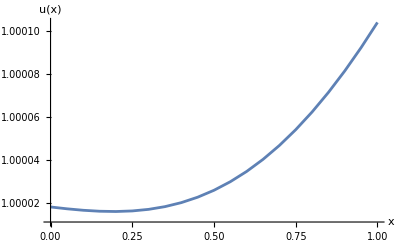

```mathematica
PlotTheTest[IteData1]
```

Сводный график

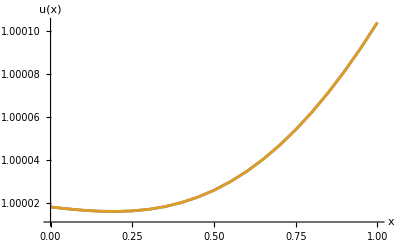

```mathematica
ComparePlotTheTest[IteData1, QuaData1]
```

Тест 2

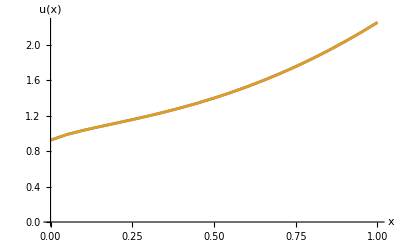

```mathematica
QuaData2 = Import["QuadtratureTest2.txt", "Table"];
IteData2 = Import["IterativeTest2.txt", "Table"];
ComparePlotTheTest[IteData2, QuaData2]
```

Тест 3

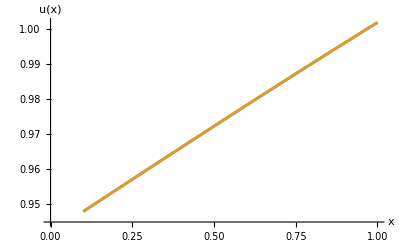

```mathematica
QuaData3 = Import["QuadtratureTest3.txt", "Table"];
IteData3 = Import["IterativeTest3.txt", "Table"];
ComparePlotTheTest[IteData3, QuaData3]
```

Тест 4

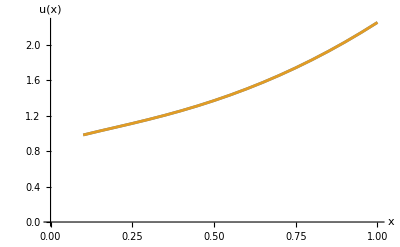

```mathematica
QuaData4 = Import["QuadtratureTest4.txt", "Table"];
IteData4 = Import["IterativeTest4.txt", "Table"];
ComparePlotTheTest[IteData4, QuaData4]
```

## Тест вырожденного ядра

Вырожденное ядро

```mathematica
(*y[x]-2Integrate[(Sin[2π(x-s)]-2)y[s],{s,0,1}]==5x*)
ysol = 5/(2π)Sin[2π x] + 5/(2π)Cos[2π x] + 5x - 2;
FullSimplify[ysol-2Integrate[(Sin[2π(x-s)]-2)(ysol/.x->s),{s,0,1}]==5x]
```

True

```mathematica
DegData1 = Import["DegenerateTest1.txt", "Table"];
```

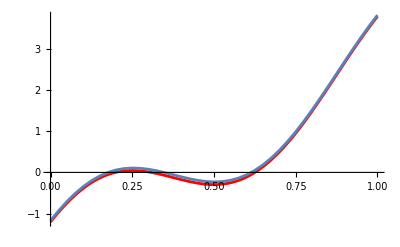

```mathematica
Show[Plot[ 5/(2π)Sin[2π x] + 5/(2π)Cos[2π x] + 5x - 2,{x,0,1},PlotStyle->Red],PlotTheTest[DegData1]]
```

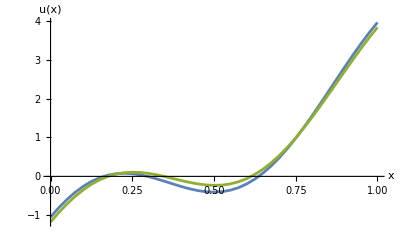

```mathematica
quadDegData1 = Import["DegenerateTest1_quad.txt", "Table"];
iterDegData1 = Import["DegenerateTest1_iter.txt", "Table"];
Compare3PlotTheTest[quadDegData1 , iterDegData1, DegData1 ]
```